# Base Bras et kets

Note :
 Quantum is a free Mathematica add - on for Dirac Bra - Ket Notation, Quantum Algebra, Quantum Computing and the QHD approximation to the Heisenberg Equations of Motion by José Luis Gómez-Muñoz and Francisco Delgado  http://homepage.cem.itesm.mx/lgomez/

```mathematica
Needs["Quantum`Notation`"];
```

### La base orthonormal des kets

Dimension de l' espace :

```mathematica
n=2;
```

```mathematica
BaseDesVecteurs=Orthogonalize[RandomInteger[{-5,5},{n,n}]]
```

{{-3/(√13),2/(√13)},{-2/(√13),-3/(√13)}}

```mathematica
|Subscript[ϕ, i_]⟩:=VectorToDirac[BaseDesVecteurs[[i]],{n}]
```

```mathematica
BaseDesKets=Table[|Subscript[ϕ, i]⟩,{i,1,n}];
```

```mathematica
BaseDesKets//Simplify
```

{(-3 |0_OverHat[1]⟩+2 |1_OverHat[1]⟩)/(√13),-(2 |0_OverHat[1]⟩+3 |1_OverHat[1]⟩)/(√13)}

```mathematica
Table[⟨Subscript[ϕ, i]|Subscript[ϕ, j]⟩,{i,1,n},{j,1,n}]//MatrixForm
```

(1 | 0
0 | 1)

### Vecteur arbitraire normal

```mathematica
VecteurArbitraire=Normalize[RandomInteger[{-5,5},{n}]]
```

{-1,0}

```mathematica
|ψ⟩=VectorToDirac[VecteurArbitraire,{n}]
```

-|0_OverHat[1]⟩

```mathematica
‖|ψ⟩‖//Simplify
```

1

### Les composantes

### Opérateur unitaire

```mathematica
Λ=∑_(n=0)^∞ |Subscript[n, OverHat[1]]⟩·⟨Subscript[n, OverHat[1]]|;
```

```mathematica
Λ·|ψ⟩//Simplify
```

-|0_OverHat[1]⟩

```mathematica
Table[DiracToVector[Λ·|ψ⟩,{Table[Subscript[i, OverHat[1]],{i,0,n-1}]}],{i,0,n-1}]//Simplify
```

{{-1,0},{-1,0}}

```mathematica
Subscript[c, i_]:=⟨Subscript[ϕ, i]|ψ⟩
```

```mathematica
Table[Subscript[c, i],{i,1,n}]//Simplify
```

{3/(√13),2/(√13)}

```mathematica
P[i_]:=(‖⟨Subscript[ϕ, i]|ψ⟩‖)^2
```

```mathematica
(*∑_(i=1)^n P[i]//Simplify//N*)
```

```mathematica
Table[{i,N[P[i],2]},{i,1,n}]//TableForm
```

1 | 0.69
2 | 0.31

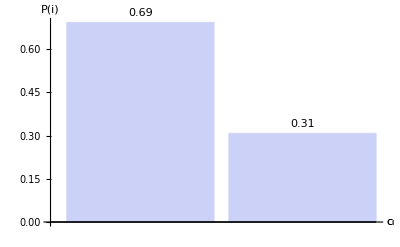

```mathematica
BarChart[Table[N[P[i],2],{i,n}],LabelingFunction->Above,AxesLabel->{"c_i","P(i)"},ChartLabels->a]
```

```mathematica
⟨ψ|·Λ·|ψ⟩
```

1